```mathematica
(**********************************************************************************)
```

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
inputfile=OpenRead["search-random-camb.txt"]
```

InputStream[…]

```mathematica
data=ReadList[inputfile,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
Close[inputfile]
```

search-random-camb.txt

```mathematica
ndata=Length[data]
```

1762

```mathematica
arrayombh2=Table[data[[i,1]],{i,1,ndata}];
```

```mathematica
arrayomch2=Table[data[[i,2]],{i,1,ndata}];
```

```mathematica
arrayhubble=Table[data[[i,3]],{i,1,ndata}];
```

```mathematica
arraymyparameter3=Table[data[[i,6]],{i,1,ndata}];
```

```mathematica
arraychi2=Table[data[[i,11]],{i,1,ndata}];
```

```mathematica
arrayomch2hubblechi2=Table[{arrayombh2[[i]],arrayhubble[[i]],arraychi2[[i]]},{i,1,ndata}];
```

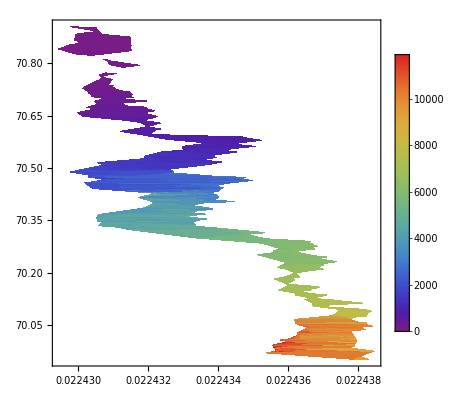

```mathematica
ListDensityPlot[arrayomch2hubblechi2,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

ListDensityPlot::prng: Value of option PlotRange -> {{0,12000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

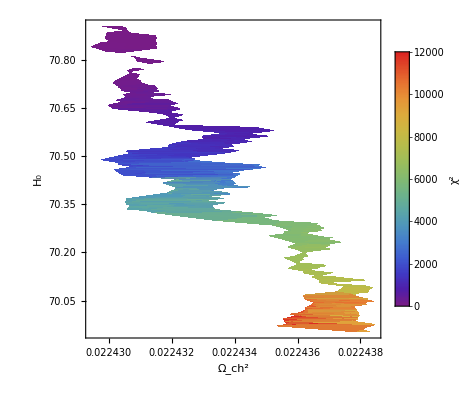

```mathematica
ListDensityPlot[arrayomch2hubblechi2,PlotRange->{{0,12000}},ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{0,12000}},LegendLabel->"χ^2"],PlotTheme->"Scientific",Frame->True,FrameStyle->{Black,Bold},FrameLabel->{"Ω_ch^2","H_0"},ImageSize->400,AspectRatio->1]
```

```mathematica
arraymyparameter3hubblechi2=Table[{arraymyparameter3[[i]],arrayhubble[[i]],arraychi2[[i]]},{i,1,ndata}];
```

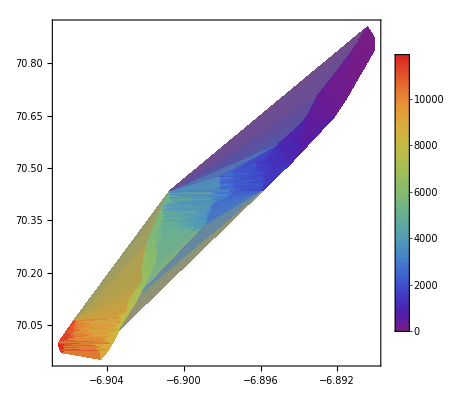

```mathematica
ListDensityPlot[arraymyparameter3hubblechi2,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

ListDensityPlot::prng: Value of option PlotRange -> {{0,12000}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

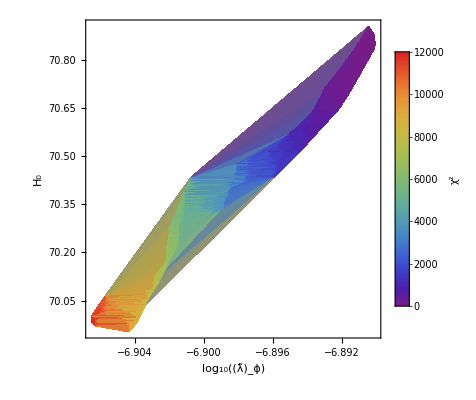

```mathematica
ListDensityPlot[arraymyparameter3hubblechi2,PlotRange->{{0,12000}},ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{0,12000}},LegendLabel->"χ^2"],PlotTheme->"Scientific",Frame->True,FrameStyle->{Black,Bold},FrameLabel->{"log_10((λ̃)_ϕ)","H_0"},ImageSize->400,AspectRatio->1]
```

```mathematica
(**********************************************************************************)
```